# The Stabilizer Formalism, by Computation

This document teaches the stabilizer formalism the way one would teach it at a chalkboard with a kernel open: every claim is immediately computed. We start from the observation that a single qubit can be specified not by its two amplitudes but by the one operator that fixes it, build that idea into the Aaronson-Gottesman tableau, and ride it all the way to thousand-qubit Clifford circuits, error-correcting codes, graph states, magic states, and Clifford channels. We close with a measured, honest comparison against the specialized C++ and Julia stabilizer simulators.

The arc is: a state is what stabilizes it (single qubit), n generators replace 2^n amplitudes (the tableau), entanglement and measurement become linear algebra over 𝔽_2 (the field of two elements {0, 1} with all arithmetic done mod 2, so that 1+1=0 and vector addition is the bitwise XOR), and then scale, codes, and the frontier. The audience is graduate students who know quantum mechanics and the Pauli group but have not yet seen why a stabilizer state of a thousand qubits is something you can hold in your hand. Everything below is built explicitly so you can change it, break it, and extend it. The Wolfram QuantumFramework symbols we exercise live in the Wolfram QuantumFramework paclet; the central one is PauliStabilizer.

## Setup

We load the framework from the working tree so the fast paths and recent fixes are present. On a current release, the plain Needs line alone suffices.

```mathematica
PacletDirectoryLoad["/Users/mohammadb/Documents/GitHub/QuantumFramework/QuantumFramework"];
Needs["Wolfram`QuantumFramework`"]
```

## The core functions at a glance

Before the narrative, the whole working surface, grouped by task. Every call is exercised in context later; this is the map.

Construct a register, from signed Pauli strings, a named code, or a random Clifford: PauliStabilizer[n], PauliStabilizer[{"XX", "ZZ"}], PauliStabilizer["SteaneCode"], PauliStabilizer["Random"[n]].

Apply a Clifford gate one at a time: ps["H", j], ps["S", j], ps["CNOT", j, k], ps["CZ", j, k], ps["SWAP", j, k].

Apply a whole circuit as a gate list, routed through the compiled engine (bare names take default targets, -> sets explicit ones): ps[{"H", "CNOT", "CNOT" -> {2, 3}}].

Inspect: ps["Stabilizers"], ps["Tableau"], ps["Matrix"], ps["State"].

Measure: ps["M", q], ps["M", "ZZ"], ps["Expectation", "ZZ"], ps["SymbolicMeasure", q].

Entanglement entropy across a cut: ps["Entropy", {1, 2}].

Sibling heads: StabilizerFrame, CliffordChannel, GraphState with LocalComplement, and the predicate StabilizerStateQ.

## Why stabilizers: the exponential wall

A pure state of n qubits is a unit vector in ℂ^(2^n), so writing it down means storing 2^n complex amplitudes. At n=20 that is already a million numbers; at n=50 it is about 10^15, a petabyte of amplitudes even at one byte each; by n=100 it passes the number of atoms in a building (∼10^30). Yet many of the states we care most about, including every state any error-correcting code protects, are not generic: they sit at the fixed points of a large group of Pauli operators, and that structure can be stored in O(n^2) bits.

To feel the wall, ask for the dense state vector of a 20-qubit GHZ state and look only at its length:

```mathematica
Length @ QuantumState["GHZ"[20]]["StateVector"]
```

1048576

That is 2^20 amplitudes for a state that, as we will see, is pinned down completely by 20 short Pauli strings. The stabilizer formalism is the bookkeeping that exploits exactly this gap.

## A state is what fixes it: the single qubit

The central move is to stop describing a state by its amplitudes and start describing it by the operators that leave it invariant. The state 0 is the unique +1 eigenvector of the Pauli operator Z. We say Z stabilizes 0, and since one operator already determines a one-qubit state up to normalization, that single fact is the state.

A caution that defines the whole subject: this works only for special states. Of all one-qubit pure states, exactly six are +1 eigenstates of a Pauli: 0 and 1 for ±Z, ± for ±X, and i for ±Y. These six are the stabilizer states, and the formalism is exactly their theory and its multi-qubit generalization; a generic cosθ0+sinθ1 is fixed by no Pauli and falls outside it. What makes the restriction worth a whole subject is that the states it does cover, as the next sections show, include the ones error correction and large parts of quantum algorithms are built from.

Verify that Z fixes 0, recalling that the built-in PauliMatrix[1], PauliMatrix[2], PauliMatrix[3] are X, Y, Z:

```mathematica
PauliMatrix[3] . {1, 0} == {1, 0}
```

True

In the framework, the one-qubit register 0 is PauliStabilizer[1]. The object prints as a summary box that shows its generators and, for small systems, its tableau, so the cheap representation is the thing you see:

```mathematica
PauliStabilizer[1]
```

PauliStabilizer[…]

We read off the operator that stabilizes it with the "Stabilizers" property:

```mathematica
PauliStabilizer[1]["Stabilizers"]
```

{Z}

The answer is the single Pauli string "Z", exactly as the chalkboard argument predicted. The "State" property is the bridge back to the rest of the framework: it materializes the stabilizer object into a full QuantumState, at the cost of the 2^n blow-up the formalism exists to avoid.

```mathematica
PauliStabilizer[1]["State"]
```

QuantumState[…]

What comes back is an ordinary QuantumState object, so a stabilizer state drops straight into the rest of the framework. Chaining "StateVector" on that object reads off the raw 2^n amplitudes, here the single column 0:

```mathematica
PauliStabilizer[1]["State"]["StateVector"] // Normal
```

{1,0}

Different states are fixed by different operators. The state +=(0+1)/√2 is the +1 eigenstate of X, and a Hadamard turns one into the other. Apply H to 0 and read the new stabilizer:

```mathematica
PauliStabilizer[1]["H", 1]["Stabilizers"]
```

{X}

The stabilizer flips from Z to X, the signature of +. The state vector confirms it:

```mathematica
PauliStabilizer[1]["H", 1]["State"]["StateVector"] // Normal
```

{1/(√2),1/(√2)}

The same move with X in place of H carries 0 to 1, and here a sign appears for the first time: 1 is the +1 eigenstate of -Z, not of Z.

```mathematica
PauliStabilizer[1]["X", 1]
```

PauliStabilizer[…]

Reading off the stabilizer makes the sign explicit:

```mathematica
PauliStabilizer[1]["X", 1]["Stabilizers"]
```

{-Z}

The answer is the signed string "-Z", the operator that fixes 1. The sign is part of the stabilizer data, which is exactly why the formalism can tell 0 from 1 even though the same unsigned Z pins both.

A short word of honesty that will matter later. The tableau tracks the stabilizer group, including the signs, but it is blind to the overall phase of the state. Reconstructing a state vector from a gate-updated tableau is therefore exact only up to a global phase. You can see this by acting with Z on +: physically Z+=-, and the framework returns - up to an overall sign.

```mathematica
PauliStabilizer[1][{"H", "Z"}]["State"]["StateVector"] // Normal
```

{-1/(√2),1/(√2)}

For everything observable, probabilities, expectation values, entanglement, the global phase is irrelevant, so this costs us nothing in practice. We flag it now because it is the one place where the cheap representation is genuinely less informative than the dense one.

Before moving on, the essentials so far:

A one-qubit stabilizer state is named by the single Pauli operator that fixes it: Z for 0, X for +, -Z for 1.

PauliStabilizer carries that operator, not the amplitudes; the "State" property hands back a full QuantumState on demand, and "StateVector" on that object gives the raw 2^n amplitudes.

The reconstructed vector is exact up to a global phase, which never affects an observable.

## The tableau: n generators instead of 2^n amplitudes

For n qubits the idea scales because the stabilizer group is generated by just n commuting, independent Pauli strings, and each Pauli string of length n is two bits per qubit: an X-exponent and a Z-exponent, since Y=iXZ. So a stabilizer state is a binary matrix of shape n×2n together with n signs, which is O(n^2) bits in place of 2^n amplitudes. This binary (X|Z) encoding is the symplectic representation of the Pauli group.

Look at the two-qubit register 00. The object itself previews the generators and a tableau grid:

```mathematica
PauliStabilizer[2]
```

PauliStabilizer[…]

The raw symplectic data is "Tableau", a rank-3 array stacking the X block above the Z block (shape 2×n×2n, here 2×2×4: two blocks, n=2 qubits, 2n=4 rows):

```mathematica
PauliStabilizer[2]["Tableau"]
```

{{{1,0,0,0},{0,1,0,0}},{{0,0,1,0},{0,0,0,1}}}

Its dimensions confirm the {2, n, 2n}={2, 2, 4} layout directly:

```mathematica
PauliStabilizer[2]["Tableau"] // Dimensions
```

{2,2,4}

The same content reads more easily flattened to a binary matrix. Each row is one generator written across as (x_1…x_n|z_1…z_n): the left half of the columns are the X-exponents, the right half the Z-exponents. For 00 it comes out as the 2n×2n identity:

```mathematica
PauliStabilizer[2]["Matrix"] // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

There is a subtlety worth pausing on: the matrix has 2n rows, not n, because the framework keeps two interleaved bases. The bottom n rows are the stabilizer generators proper, the operators that fix the state; the top n are destabilizer generators, a symplectic-dual partner basis introduced by Aaronson and Gottesman, each anticommuting with exactly one stabilizer and commuting with all the rest. The destabilizers cost nothing asymptotically and turn measurement from an exponential search into an O(n^2) tableau update, as we will see.

The rows are bits, but each one decodes back to a signed Pauli string, and pairing them makes the correspondence concrete. Read in storage order, destabilizers first and then stabilizers:

```mathematica
MapThread[Rule, {
   PauliStabilizer[2]["Matrix"],
   Join[PauliStabilizer[2]["Destabilizers"], PauliStabilizer[2]["Stabilizers"]]
}] // Column
```

{1,0,0,0}→XI
{0,1,0,0}→IX
{0,0,1,0}→ZI
{0,0,0,1}→IZ

Row {1, 0,0, 0} is the destabilizer X_1, an X on qubit 1 (the string "XI"); row {0, 0,1, 0} is the stabilizer Z_1 ("ZI"); and so on. Now the identity pattern is transparent: for 00 every destabilizer is a single X, a lone 1 in the left half, and every stabilizer a single Z, a lone 1 in the right half.

One ordering trap to flag: the standalone "PauliStrings" property lists the stabilizers first and the destabilizers second, the reverse of the storage row order above.

```mathematica
PauliStabilizer[2]["PauliStrings"]
```

{ZI,IZ,XI,IX}

So the first n entries are the stabilizers (Z_1, Z_2) and the last n are their destabilizer partners (X_1, X_2).

The header promised that these n generators are the state, so the inverse map back to the 2^n amplitudes should be explicit, and it is. A stabilizer state is the simultaneous +1 eigenvector of its generators. Equivalently, the projector onto their joint +1 eigenspace,

P = ∏_i (𝟙+s_i g_i)/2,

is rank one, P=ψψ, so any nonzero column of P is the state up to normalization. Here g_i is the i-th stabilizer generator as a 2^n×2^n Pauli matrix and s_i∈{+1, -1} its sign, both read off the tableau (the "Stabilizers" strings above). Building P and taking its nonzero column reconstructs 00 by hand, in two steps. The matrix of a Pauli string is just QuantumOperator[s]["Matrix"] (for instance QuantumOperator["ZI"]["Matrix"] is Z⊗I), so no custom decoder is needed.

First, build the projector P=∏_i (𝟙+s_i g_i)/2 by multiplying the single-generator projectors (𝟙+g_i)/2 over the two stabilizers (ZI and IZ). For 00 it collapses to 0000, a rank-one matrix with a single 1 in the corner:

```mathematica
(codeProjector = Dot @@ ((IdentityMatrix[4] + QuantumOperator[#]["Matrix"]) / 2 & /@ PauliStabilizer[2]["Stabilizers"])) // MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Second, read the state off P. Because P=ψψ, every nonzero column is proportional to the state, so Transpose exposes the columns as rows, Select keeps the first nonzero one, and Normalize fixes its length:

```mathematica
reconstructed = Normalize @ First @ Select[Transpose[codeProjector], AnyTrue[#, # != 0 &] &]
```

{1,0,0,0}

This is exactly the vector the "State" property returns, the O(2^n) computation the cheap representation exists to postpone:

```mathematica
reconstructed === (PauliStabilizer[2]["State"]["StateVector"] // Normal)
```

True

The construction is not special to product states: the same lines turn the two generators XX and ZZ into the entangled Bell amplitudes (1,0,0,1)/√2, the state the next section builds from gates.

```mathematica
Normalize @ First @ Select[
   Transpose[Dot @@ ((IdentityMatrix[4] + QuantumOperator[#]["Matrix"]) / 2 & /@ {"XX", "ZZ"})],
   AnyTrue[#, # != 0 &] &
]
```

{1/(√2),0,0,1/(√2)}

It is worth pausing on what these states look like in general, because the picture is simple. Every stabilizer state is a flat superposition: its nonzero amplitudes all share a single magnitude, up to signs and factors of i, and they sit on an affine subspace of 𝔽_2^n, the solution set of the Z-type parity checks in the stabilizer group. A three-qubit example shows the anatomy directly. Build it:

```mathematica
psAffineDemo = PauliStabilizer[3][{"H", "H" -> {2}, "CNOT" -> {1, 3}, "CNOT" -> {2, 3}}]
```

PauliStabilizer[…]

and read off its amplitudes:

```mathematica
psAffineDemo["State"]["StateVector"] // Normal
```

{1/2,0,0,1/2,0,1/2,1/2,0}

Four of the eight amplitudes are 1/2 and the rest vanish. The support {000, 011,101, 110} is exactly the even-parity strings x_1⊕x_2⊕x_3=0, a two-dimensional subspace of 𝔽_2^3 cut out by the generator ZZZ. That ZZZ really sits in the stabilizer group shows up as a +1 expectation value:

```mathematica
psAffineDemo["Expectation", "ZZZ"]
```

1

That is the whole anatomy of a stabilizer state: a uniform superposition over a coset, with the relative signs fixed by the generator signs. The exponential compression is now intuitive: naming the subspace and the signs costs O(n^2) bits, while listing the amplitudes costs 2^n.

Why is any of this fast? Because of what a Clifford gate is: precisely a unitary that conjugates every Pauli to a Pauli, that is, an element of the normalizer of the Pauli group. The Hadamard, the phase gate S, and CNOT generate the whole Clifford group, and they are exactly the gates the tableau handles. Updating the state therefore means updating each generator, g↦Ug U^†, which is a fixed local rewrite of two bits and a sign per affected qubit. This is the content of the Gottesman-Knill theorem: a circuit of Clifford gates on a stabilizer input can be simulated in time polynomial in n, with O(n) work per gate, rather than the O(2^n) of dense state-vector evolution. The single-qubit gate methods ("H", "S", "X", "Y", "Z", "V" for √X, and SuperDagger["S"]) and the two-qubit "CNOT", "CZ", "SWAP" each perform exactly that rewrite.

## Two pictures of one circuit: Schrödinger and Heisenberg

That rewrite is worth slowing down on, because it is the whole reason the formalism reproduces ordinary quantum mechanics on its domain. The standard task is concrete: given a circuit, produce the final state. There are two ways to do it. The Schrödinger way carries the state vector forward, ψ↦Uψ, with 2^n amplitudes evolving under 2^n×2^n matrices. The Heisenberg way carries the generators forward and never forms the state at all. They return the same state, and watching them meet is the clearest way to see what the tableau computes.

Fix a small Clifford circuit on three qubits, with an S gate to make the result nontrivial:

```mathematica
cliffordCircuit = QuantumCircuitOperator[{"H" -> 1, "CNOT" -> {1, 2}, "S" -> 2, "CNOT" -> {2, 3}}]
```

QuantumCircuitOperator[…]

Its diagram makes the gate order visible:

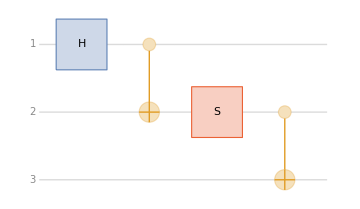

```mathematica
cliffordCircuit["Diagram"]
```

In the Schrödinger picture we propagate 000 through the circuit, keeping the resulting QuantumState object (we reuse it below):

```mathematica
psiSchrodinger = cliffordCircuit[QuantumState["000"], Method -> "Schrodinger"]
```

QuantumState[…]

Its amplitudes are the answer the formalism has to reproduce:

```mathematica
psiSchrodinger["StateVector"] // Normal
```

{1/(√2),0,0,0,0,0,0,ⅈ/(√2)}

The state is (000+i111)/√2, a GHZ-type state carrying the relative phase the S gate inserted.

Now the Heisenberg picture. Instead of asking where the state goes, ask what fixes it. If g stabilizes ψ, then after a gate U the conjugated operator Ug U^† stabilizes Uψ, because gψ=ψ gives (Ug U^†)Uψ=Ugψ=Uψ. The whole evolution of the state is therefore carried by the conjugation g↦Ug U^† of its generators, and the one fact that makes this cheap is that a Clifford sends a Pauli to a Pauli. Take the input generator Z_1 and conjugate it by the circuit, U Z_1 U^†. Writing that conjugation as a circuit that applies U^†, then Z_1, then U (the same conjugation-as-a-circuit idiom the T example below uses), "PauliDecompose" reads off the result:

```mathematica
QuantumCircuitOperator[{cliffordCircuit["Dagger"], "Z" -> 1, cliffordCircuit}]["PauliDecompose"]
```

<|XYX→1|>

The decomposition has a single term, X_1 Y_2 X_3: the operator never left the Pauli group. One generator went in, one came out. That closure is why the tableau update of the previous section is a fixed local rewrite of a few bits rather than a dense matrix multiply.

Propagating all three input generators Z_1, Z_2, Z_3 this way is exactly what the stabilizer backend does. Running the same circuit object with Method -> "Stabilizer" in place of "Schrodinger" returns the stabilizer group of the final state, whose first generator is the X_1 Y_2 X_3 we just conjugated by hand:

```mathematica
cliffordCircuit[QuantumState["000"], Method -> "Stabilizer"]["Stabilizers"]
```

{XYX,ZZI,IZZ}

The two pictures must describe the same physics, and they do. Materialize the state from the final generators (the formalism's "State"):

```mathematica
psiStabilizer = cliffordCircuit[QuantumState["000"], Method -> "Stabilizer"]["State"]
```

QuantumState[…]

Its amplitudes match the Schrödinger answer up to a global phase, here a factor of i:

```mathematica
psiStabilizer["StateVector"] // Normal
```

{-ⅈ/(√2),0,0,0,0,0,0,1/(√2)}

Rather than chase that phase by hand, compare the two states with the framework's QuantumSimilarity, which is one exactly when they agree up to a global phase:

```mathematica
QuantumSimilarity[psiSchrodinger, psiStabilizer]
```

1

This is the Gottesman-Knill theorem made concrete: a Clifford circuit on a stabilizer input is simulated by propagating n generators at O(n) work per gate, and the state it computes is exactly the one Schrödinger evolution would, with the 2^n vector never formed except, here, to check.

The construction rests entirely on Clifford conjugation keeping a Pauli a Pauli, so it is also clear where it must break. A non-Clifford gate does not respect the Pauli group. The T gate commutes with Z, but conjugating X by it gives a sum. The conjugation TX T^† is cleanest as the circuit {T^†, X, T} decomposed into Paulis:

```mathematica
ExpToTrig @ QuantumCircuitOperator[{SuperDagger["T"], "X", "T"}]["PauliDecompose"]
```

<|X→1/(√2),Y→1/(√2)|>

Here TX T^†=(X+Y)/√2 has two terms, not one. A single generator no longer maps to a single generator, the group stops being generated by n Pauli strings, and the cheap representation fails. That failure is not an accident of implementation but the edge of the classically tractable world; the frontier section returns to how far one can push past it with stabilizer frames.

## Entanglement for free: Bell and GHZ

Entangled states are not special in this language; they are simply stabilizer groups whose generators are not single-qubit operators. The Bell state Φ^+ is prepared from 00 by a Hadamard and a CNOT, and its stabilizer group is generated by XX and ZZ.

Build the Bell state:

```mathematica
bell = PauliStabilizer[2][{"H", "CNOT"}]
```

PauliStabilizer[…]

and read its generators:

```mathematica
bell["Stabilizers"]
```

{XX,ZZ}

The generators XX and ZZ are the familiar parity checks: the two qubits share an X-parity and a Z-parity, which is precisely what maximal entanglement looks like here. The state vector is the textbook one:

```mathematica
bell["State"]["StateVector"] // Normal
```

{1/(√2),0,0,1/(√2)}

Entanglement entropy, normally a Schmidt-decomposition computation that blows up with system size, has a closed form for stabilizer states. Fattal and collaborators showed that the entanglement entropy across a cut A equals the 𝔽_2-rank of the generators restricted to A (for each generator keep only the symplectic columns of the qubits in A), minus |A|. The framework computes this with "Entropy", in O(n^3) and with no dependence on |A|. For the Bell state, tracing out one qubit gives one bit of entropy:

```mathematica
bell["Entropy", {1}]
```

1

The payoff is scale. A GHZ state on a thousand qubits is built by one Hadamard and a ladder of CNOTs. Build it (the object prints as a compact summary, never forming a 2^1000 vector):

```mathematica
ghz = PauliStabilizer[1000][Prepend[Table["CNOT" -> {q - 1, q}, {q, 2, 1000}], "H"]]
```

PauliStabilizer[<|Signs -> {1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, «1887», 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1, 1}, «1»|>]

Its single-qubit entanglement entropy is still one bit:

```mathematica
{ghz["Qubits"], ghz["Entropy", {1}]}
```

{1000,1}

Time the entropy of this thousand-qubit GHZ state to see that it is essentially instantaneous:

```mathematica
AbsoluteTiming[ghz["Entropy", {1}]]
```

{0.528185,1}

What we have established:

An entangled stabilizer state is one whose generators are multi-qubit Pauli strings; Bell is ⟨XX, ZZ⟩.

Entanglement entropy is an 𝔽_2 rank, computable at n=1000 in milliseconds.

The cost of all this is O(n^2) storage and O(n^3) for the rank, never O(2^n).

## Measurement: randomness, back-action, and correlation

Measurement is where the destabilizers earn their keep. Measuring Z on qubit a splits into two cases. If Z_a commutes with every stabilizer, then ±Z_a already lies in the stabilizer group: the outcome is deterministic, the state is unchanged, and the bit is the sign of the generator product that equals Z_a, which the destabilizers locate in O(n^2). If instead some stabilizer anticommutes with Z_a, the outcome is a fair coin, and the post-measurement state follows from a sequence of Aaronson-Gottesman row sums into one anticommuting generator, with a destabilizer as scratch. Either way the work is O(n^2), never O(2^n).

A measurement on a stabilizer state returns an association from outcome to post-state. For the Bell state, measuring qubit 1 is random, so both branches appear:

```mathematica
bell["M", 1]
```

<|0→PauliStabilizer[…],1→PauliStabilizer[…]|>

The two values are the post-measurement stabilizer states for outcomes 0 and 1; their signs differ, which is the collapse. The correlation that makes the Bell state interesting shows up when we measure every qubit of a GHZ state: only the all-zeros and all-ones strings have nonzero probability.

```mathematica
ghz3 = PauliStabilizer[3][{"H", "CNOT", "CNOT" -> {2, 3}}]
```

PauliStabilizer[…]

Measure all three qubits and keep just the outcome keys:

```mathematica
Keys[ghz3["M", {1, 2, 3}]]
```

{{0,0,0},{1,1,1}}

The outcomes are exactly {0, 0, 0} and {1, 1, 1}: the GHZ state never returns a split string with some 0s and some 1s, which is the perfect three-body correlation. We can also measure a joint Pauli observable directly, for instance the parity ZZ on the Bell state, which is deterministic and equal to +1:

```mathematica
bell["M", "ZZ"]
```

<|0→PauliStabilizer[…]|>

The single key tells us the ZZ parity is certain. The same fact, as an expectation value, comes from "Expectation", which tracks the Aaronson-Gottesman i-powers in closed form and returns ±1 or 0:

```mathematica
{bell["Expectation", "ZZ"], bell["Expectation", "XX"], bell["Expectation", "ZI"]}
```

{1,1,0}

The parities ZZ and XX are certain (+1), while a single-qubit Z is maximally uncertain (0), the hallmark of an entangled state whose marginals are maximally mixed.

There is a more efficient way to handle many shots, and it exposes something the branching picture hides. The Association ps["M", q] is the honest per-shot view, but it scales badly: a circuit with r random measurements has a tree of up to 2^r outcome branches, so gathering statistics that way means either expanding the whole tree or re-traversing the circuit once per sample. The SymPhase technique of Fang and Ying replaces the branching with bookkeeping. The circuit is traversed once, and each unresolved random outcome is recorded as a fresh formal bit s_k written into a sign, leaving the state a single PauliStabilizer. A symbolic Z-measurement of Bell qubit 1 introduces one such bit:

```mathematica
sm = PauliStabilizer[2][{"H", "CNOT"}]["SymbolicMeasure", 1]
```

PauliStabilizer[…]

Its generators now carry the formal outcome in a sign:

```mathematica
sm["Stabilizers"]
```

{1 - 2*s[1]*ZI,ZZ}

The sign of the first generator is now 1-2 s_1, which is +1 at s_1=0 and -1 at s_1=1: the formal bit is the unmade measurement. (The subscript on s_k is a running session counter, so measuring again or re-running these cells allocates s_2, s_3, ….) Substituting a concrete value resolves it, and the two substitutions give exactly the two branches we saw above:

```mathematica
{sm["SubstituteOutcomes", {s[1] -> 0}]["Stabilizers"],
 sm["SubstituteOutcomes", {s[1] -> 1}]["Stabilizers"]}
```

{{ZI,ZZ},{-ZI,ZZ}}

The first reason to care is that the single symbolic traversal then serves arbitrarily many shots. The "SampleOutcomes" property draws samples by substituting random bits for the formal ones, never re-running the H-CNOT circuit; a thousand shots of the qubit-1 outcome come out a fair coin:

```mathematica
SeedRandom[7];
Counts[(1 - #["StabilizerSigns"][[1]]) / 2 & /@ sm["SampleOutcomes", 1000]]
```

<|1→492,0→508|>

The second reason is that the formal bits thread through the rest of the circuit, so correlations between outcomes are carried into the samples rather than discarded with the branch structure. Measure all three qubits of the GHZ state symbolically, sample a thousand shots, and read off the bit-strings: every shot is 000 or 111, the perfect three-body correlation, reproduced from one traversal.

A small helper reads the bit-string a sample collapses to, by locating its one nonzero amplitude:

```mathematica
readBits[ps_] := IntegerDigits[FirstPosition[Normal[ps["State"]["StateVector"]], x_ /; x != 0][[1]] - 1, 2, ps["Qubits"]]
```

Measure all three qubits symbolically, in one traversal:

```mathematica
smGHZ = ghz3["SymbolicMeasure", {1, 2, 3}]
```

PauliStabilizer[…]

Then draw a thousand shots and tally the bit-strings: only the two correlated outcomes ever appear.

```mathematica
SeedRandom[7];
Counts[readBits /@ smGHZ["SampleOutcomes", 1000]]
```

<|{1,1,1}→492,{0,0,0}→508|>

This is the payoff of carrying symbols instead of branching: the circuit traversal is paid for once, and any number of correlated shots then follow by cheap substitution. It is the in-language, exact-arithmetic cousin of the bulk Pauli-frame samplers the dedicated engines use for the same purpose, which the closing comparison returns to.

## Scaling up: random Cliffords and compiled circuits

Sampling a Clifford operation uniformly at random is a basic primitive for randomized benchmarking and for probing the typical entanglement of stabilizer states. The framework implements the Bravyi-Maslov construction via the Koenig-Smolin Mallows-distribution sampler, exposed as PauliStabilizer["Random"[n]]. Sampling a random 200-qubit Clifford state and confirming it is a genuine stabilizer state is immediate:

```mathematica
SeedRandom[42];
AbsoluteTiming[StabilizerStateQ[PauliStabilizer["Random"[200]]]]
```

{0.075663,True}

That random state arrives as a bare tableau, with no circuit attached. The "Circuit" property hands one back: an explicit Clifford circuit that prepares the state from 0…0, by the Aaronson-Gottesman canonical decomposition. Unlike the membership test above, this direction has real cost: the synthesis is O(n^3) gates and is not length-minimized, so it is a moderate-n tool rather than a thousand-qubit one. On a ten-qubit random Clifford it is immediate. Sample one:

```mathematica
SeedRandom[11];
ps10 = PauliStabilizer["Random"[10]]
```

PauliStabilizer[…]

Read off its preparation circuit with the "Circuit" property (a hundred-plus-gate object, so we hold it in prep rather than print it):

```mathematica
prep = ps10["Circuit"];
```

then confirm its head and polynomial gate count:

```mathematica
{Head[prep], Length @ QuantumShortcut[prep]}
```

{QuantumCircuitOperator,136}

The result is an ordinary QuantumCircuitOperator. It genuinely builds the state: applied to the all-zeros register it reproduces ψ exactly. At ten qubits a full QuantumSimilarity would form a 2^10×2^10 density matrix, so here we take the cheaper direct state-vector overlap, whose magnitude is one:

```mathematica
Chop[Abs[Conjugate[Normal @ prep[]["StateVector"]] . Normal @ ps10["State"]["StateVector"]] - 1]
```

0

This is the inverse of the gate-folding below, which goes from circuit to tableau, and it is the workhorse behind code encoders: a code state's preparation circuit is exactly its encoding circuit.

For long Clifford circuits the framework folds the entire gate list through a single compiled (C) kernel that operates on a bit-packed, generator-major tableau, the same data layout the specialized simulators use. Handing the whole gate list to ps[gates] folds it in one such pass. First build a four-thousand-gate random Clifford stream on two hundred qubits (kept suppressed, since it is four thousand gate specs):

```mathematica
SeedRandom[1];
specs = Table[
   RandomChoice[{"H" -> RandomInteger[{1, 200}], "S" -> RandomInteger[{1, 200}],
     "CNOT" -> RandomSample[Range[200], 2]}],
   {4000}];
```

then fold it and watch the wall-clock:

```mathematica
AbsoluteTiming[PauliStabilizer[200][specs]["Stabilizers"][[1]]]
```

{0.034515,-XYIYZIIZZIXIIZZIYZIZIXYXIXYIXYZZXYXXYIIZZXIXXYIZXYIZYIXIYZZYIIXXZIIXXZYYYZZIXYZIYZIXIYYYYZIXXXYXZZXXXZIIXZIIIIZXYYYXXYXXYXIXXZIZYIXZZXYZZIYIXZXXXIIXZXIYZZYIXIXZXXIIZIYIYXIIXIYXYZYZYIXZYIIZXIYIIZIZXZIZ}

That is roughly a quarter of a microsecond per gate, flat in the number of qubits, because each gate touches only the machine words of its own column. The same engine backs the circuit object: a QuantumCircuitOperator applied with Method -> "Stabilizer" evolves a stabilizer state directly. Build a Bell circuit:

```mathematica
qc = QuantumCircuitOperator[{"H" -> 1, "CNOT" -> {1, 2}}]
```

QuantumCircuitOperator[…]

run it through the stabilizer backend:

```mathematica
r = qc[QuantumState["00"], Method -> "Stabilizer"]
```

PauliStabilizer[…]

and confirm the result is a PauliStabilizer with the Bell generators:

```mathematica
{Head[r], r["Stabilizers"]}
```

{PauliStabilizer,{XX,ZZ}}

The result is a PauliStabilizer, not a dense state. The two-pictures section earlier proved that the stabilizer and Schrödinger paths land on the same state; here is the same check at random, on a 30-gate Clifford circuit. First build the stream (suppressed, 30 gate specs):

```mathematica
SeedRandom[7];
specs2 = Table[
   RandomChoice[{"H" -> RandomInteger[{1, 4}], "S" -> RandomInteger[{1, 4}],
     "CNOT" -> RandomSample[Range[4], 2]}],
   {30}];
```

Run it densely:

```mathematica
dense = QuantumCircuitOperator[specs2][QuantumState["0000"], Method -> "Schrodinger"]
```

QuantumState[…]

run it in the tableau:

```mathematica
stab = PauliStabilizer[4][specs2]["State"]
```

QuantumState[…]

and compare with QuantumSimilarity:

```mathematica
QuantumSimilarity[dense, stab]
```

1

A performance caveat that is also a design lesson. The convenience constructor PauliStabilizer[circuit] converts an arbitrary circuit by Pauli-conjugating each gate through full tomography, which is exponential in the qubit count and is meant only for tiny circuits. For anything at scale, use the gate-update chain or the circuit-list form ps[gates], which stay in the tableau. The right tool for the job is the difference between milliseconds and minutes.

## Error-correcting codes as stabilizer states

Quantum error-correcting codes were the original motivation for the formalism: a code is defined by its stabilizer group, and a logical codeword is the simultaneous +1 eigenstate of the parity checks. The framework ships the canonical examples as named codes. The five-qubit perfect code is generated by four weight-four checks plus the logical Z̄:

```mathematica
PauliStabilizer["5QubitCode"]["Stabilizers"]
```

{XZZXI,IXZZX,XIXZZ,ZXIXZ,ZZZZZ}

The four cyclic permutations XZZXI, IXZZX, XIXZZ, ZXIXZ are the parity checks whose syndrome diagnoses any single-qubit error: the code has distance three, so it corrects one. The final ZZZZZ selects the logical 0_L within the code space. The Steane code, the CSS code built from the classical [7,4] Hamming code, separates cleanly into X-type and Z-type checks:

```mathematica
PauliStabilizer["SteaneCode"]["Stabilizers"]
```

{IIIXXXX,XIXIXIX,IXXIIXX,IIIZZZZ,ZIZIZIZ,IZZIIZZ,ZZZZZZZ}

The first three generators are pure X checks and the next three pure Z checks, the defining CSS structure; the seventh is again the logical Z̄. Measuring these generators on an encoded state is exactly the syndrome extraction of the previous section, and because each is a Pauli string, the measurement stays in the tableau.

## The frontier: graph states, magic, and channels

Three directions take the formalism to the edge of current research, and the framework has a head for each. This section gives each one enough room to compute with, not just name.

### Graph states

A theorem of Van den Nest and others says every stabilizer state is local-Clifford-equivalent to a graph state: place + on each vertex of a graph and apply a controlled-Z along each edge. Its stabilizer at vertex i is X_i∏_(j∼i) Z_j. Build the graph state on a 4-cycle:

```mathematica
gs = GraphState[CycleGraph[4]]
```

GraphState[…]

and read its generators:

```mathematica
gs["Stabilizers"]
```

{XZIZ,ZXZI,IZXZ,ZIZX}

Each generator is an X on one vertex dressed by Z on its neighbors, the cluster-state structure. A graph state is an ordinary stabilizer state, so it converts to a PauliStabilizer and answers the same questions. The 4-cycle cluster carries two bits of entanglement across the cut {1, 2}|{3, 4}, one per edge crossing it:

```mathematica
{StabilizerStateQ[gs["PauliStabilizer"]], gs["PauliStabilizer"]["Entropy", {1, 2}]}
```

{True,2}

The graph is a far more compact record than the tableau when the state is sparse. A path graph gives the one-dimensional cluster state of measurement-based computation, each generator a local XZ pattern:

```mathematica
GraphState[PathGraph[Range[3]]]["Stabilizers"]
```

{XZI,ZXZ,IZX}

The operation that moves through the local-Clifford equivalence class is local complementation, which toggles the edges among the neighbors of a chosen vertex; here it is [LocalComplement]. Local-complementing the 4-cycle at vertex 1 adds the edge between its two neighbors:

```mathematica
EdgeList[LocalComplement[CycleGraph[4], 1]]
```

{1<->2,1<->4,2<->3,2<->4,3<->4}

The graph is updated correctly, but the accompanying single-qubit Clifford corrections, the vertex operators that would make the equivalence exact at the state level, are not yet tracked. Use this for graph surgery rather than for exact state identity.

### Magic and stabilizer rank

Clifford gates keep us inside the stabilizer world; a non-Clifford gate such as T does not. The framework represents a state that has left the stabilizer manifold as a [StabilizerFrame], a superposition ∑_i c_i s_i of stabilizer states. As the Heisenberg section showed, T turns one Pauli into a sum of two, and at the state level that means each T gate at most doubles the number of stabilizer terms. The term count is the stabilizer rank, the quantity that controls the cost of classically simulating magic, in the sense of Bravyi and Gosset. Watch it double, gate by gate. A helper reports the term count, with a bare PauliStabilizer counting as rank 1 and a frame as its component count:

```mathematica
stabRank[x_] := If[Head[x] === StabilizerFrame, x["Length"], 1]
```

Apply k successive T gates to + and tabulate the rank:

```mathematica
Table[{k, stabRank[PauliStabilizer[1][Join[{"H"}, Table["T", k]]]]}, {k, 0, 5}]
```

{{0,1},{1,2},{2,4},{3,8},{4,16},{5,32}}

The rank goes 1,2,4, …, 2^k: the exponential cost of magic made concrete, and the reason a T-rich circuit is hard where a Clifford circuit is easy. The frame is not only a counting object. Because each component carries the Pauli that relates it coherently to a shared reference, its dense state vector is exact, matching the brute-force statevector up to a single global phase. Build the one-T frame:

```mathematica
frame = PauliStabilizer[2][{"H", "T"}]
```

StabilizerFrame[…]

compute the same state densely:

```mathematica
dense = QuantumCircuitOperator[{"H" -> 1, "T" -> 1}][QuantumState["00"], Method -> "Schrodinger"]
```

QuantumState[…]

and compare with QuantumSimilarity, which returns one for states that agree up to a global phase:

```mathematica
QuantumSimilarity[frame["State"], dense]
```

1

What the frame does not yet do is compress. The true stabilizer rank of t magic states grows like 2^αt with α≈0.4, far below the naive 2^t, and the framework keeps every term. So the frame is exact and faithful for a handful of T gates and is the right object to reason about rank, but it is not a scalable magic-state simulator; for that the terms must be merged, which is the Bravyi-Gosset program.

### Clifford channels

Open-system Clifford dynamics, the maps that send stabilizer states to stabilizer states, are encoded by a Boolean Choi tableau in the framework's [CliffordChannel], following Yashin. The identity channel on n qubits has a tableau of 2n rows:

```mathematica
CliffordChannel["Identity", 3]["Rank"]
```

6

A pure stabilizer state is itself a state-preparation Clifford channel, whose tableau is the state's stabilizer half. Converting the Bell state to its channel recovers its two parity-check rows:

```mathematica
CliffordChannel[PauliStabilizer[2][{"H", "CNOT"}]]["Tableau"] // MatrixForm
```

(1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 0)

Noise stays in the tableau too. A named Pauli channel applied to a stabilizer state returns a probability-weighted mixture of stabilizer states, each branch an O(n) tableau update rather than a dense density matrix. A bit-flip channel on 0 is the textbook example, 0 with probability 1-p and 1 with probability p:

```mathematica
{#1, #2["Stabilizers"]} & @@@ QuantumChannel["BitFlip"[1/10]][PauliStabilizer[1]]
```

{{9/10,{Z}},{1/10,{-Z}}}

The two branches are stabilized by +Z and -Z, the 0 and 1 of a classical bit flip, with weights 9/10 and 1/10.

These heads, together with PauliStabilizer and StabilizerFrame, let one stay in the tableau picture for states, codes, graph-state surgery, magic accounting, and noise, inside the same object model as the rest of the framework.

## An honest comparison with other packages

The stabilizer simulators built for raw throughput are Stim, a C++ engine, and QuantumClifford.jl, a Julia package; both are excellent and both are narrower in scope than a general quantum framework. The fair question is two-sided: how close is the framework on the task they specialize in, and what does it offer that they do not.

On gate-folding throughput the gap is now a small constant factor. The figures below are the measured wall-clock for an identical Clifford stream on an Apple M2 Pro, measured June 2026 from the framework's own bottleneck audit, with Stim for reference; treat them as a dated snapshot, not a guarantee:

qubits (gates) | QuantumFramework | Stim | ratio
100 (2k) | 2.6 ms | 1.03 ms | 2.5x
500 (10k) | 26.2 ms | 5.14 ms | 5.1x
1000 (20k) | 58.0 ms | 10.9 ms | 5.3x

At a thousand qubits the framework also runs ahead of QuantumClifford.jl on the same stream (58.0 ms against 108.4 ms). The remaining gap to Stim is SIMD lane width, Stim packs 256-bit vector lanes against the framework's 62-bit machine words, plus a small per-gate circuit-encoding pass; it is a constant factor, not an algorithmic deficit. Getting there took compiling the gate fold to a single C kernel: the gate-by-gate interpreted path is 15 to 30 times slower, around 74, 402, and 955 ms at the three sizes above.

What the framework offers that the dedicated engines do not:

Symbolic signs. Outcomes can be carried as formal symbols through a circuit (the SymPhase method), so a single traversal serves arbitrarily many samples, and outcome correlations are explicit polynomials.

Exact arithmetic. Coefficients, signs, and the random-Clifford sampler use exact rationals, so seeded output is bit-reproducible and there is no floating-point drift.

One object model. A PauliStabilizer converts to a QuantumState, a QuantumOperator, a QuantumCircuitOperator, or a QuantumChannel, so a stabilizer subroutine drops into a larger simulation that also uses dense states, density matrices, Lindblad evolution, or phase-space methods, without leaving the language.

Breadth of heads. Graph states with local complementation, stabilizer frames for magic accounting, and Clifford channels for open-system Clifford dynamics are first-class objects, not features one bolts on.

Where the framework genuinely trails, stated plainly:

It is a constant factor (roughly 2.5 to 5.3×) behind Stim on pure gate throughput, for the lane-width reason above.

It has no constant-cost bulk Pauli-frame sampler, the trick that makes Stim's shot-by-shot sampling so cheap.

Constructing a QuantumCircuitOperator with 10^4 or more gates carries host-framework overhead; for long streams one should hand the gate-spec list to ps[gates] directly.

Reconstructing an exact state vector from a gate-updated tableau, or from a gate-built stabilizer frame, is correct up to a single global phase, which is never observable; only the relative phase between two separately-built objects is gauge-limited.

The summary is the one a physicist would want: for raw Clifford throughput the specialized engines are a few times faster, and if that is the only thing one needs, they are the right tool. For stabilizer simulation that has to interoperate with the rest of a quantum-mechanics toolkit, carry symbols, stay exact, and reach into codes, graph states, magic, and channels, the framework buys all of that for a small constant in speed.

## Where this leaves us

We built the stabilizer formalism from one idea, that a state is named by what fixes it, and rode it from a single qubit to a thousand. Along the way the concrete tools were: PauliStabilizer for states, codes, and the tableau; the gate-update methods and the circuit-list form ps[gates] for Clifford evolution; "M", "Expectation", and "SymbolicMeasure" for measurement; "Entropy" for entanglement; PauliStabilizer["Random"[n]] for sampling; and GraphState, StabilizerFrame, and CliffordChannel for the frontier.

The natural next steps are the ones the formalism opens onto: syndrome decoding on the codes of the error-correction section, stabilizer-rank simulation of magic-rich circuits via the frame, and Clifford-channel models of realistic noise. Each is a short extension of the computations above, and each stays, as long as it can, inside the O(n^2) tableau that makes the whole subject tractable.

The key references underpinning the implementation are Gottesman's stabilizer-codes thesis (1997), Aaronson and Gottesman on the tableau and its measurement update (2004), Fattal and collaborators on stabilizer entanglement entropy (2004), Anders and Briegel on graph states and local complementation (2005), Koenig and Smolin on the random-Clifford sampler (2014), Garcia and Markov on stabilizer frames (2015), Fang and Ying on symbolic phases (2023), and Yashin on Clifford channels (2025).